# Tutorial 1

## Intro - Cell and cell types: this is Section

### This is subsection

#### This is subsubsection

This is text. We can use it just like a word processor

```mathematica
by default, this is Input. It is supposed to be Mathematica code that it will execute by Shift+enter
```

```mathematica
This is where one can enter code as a block. It is not that much different from Input cell above.
```

The objective of this section is to learn how to create, edit a Mathematica Notebook. If you are familiar with Jupyter notebook, you will see similarity.

## 0. A very basic note to start

In Mathematica, the most important keyboard operation is:

This is known as Shift+Enter. Hold Shift key and hit Enter. It ONLY works on an “input cell,” which is highlighted as light yellow in all these lessons. 
What does it do? it executes the codes in the selected input cell.

Same as Jupyter, R, etc. 
-Graphics-

## 1. Data and variables - basic

### 1.1 Data on the internal stack (work space)

Example of data: voltage = 5.2 volt. Here is the representation of the data

```mathematica
5.2
```

5.2

The data is stored in the “stack”. We access it with this command: %

```mathematica
%
```

5.2

It is more convenient to assign a name to a data so that we can “call” it whenever needed. This “name” represents a “variable,” and this is how a “variable” is created and assigned:

### 1.2 Assigment of value to a variable

```mathematica
voltage=5.2
```

5.2

We can make a note (comment) of its unit like this:

```mathematica
voltage=5.2 (* the unit is Volt *)
```

5.2

Or, perhaps we can define a variable with explicit undefined variable “Volt”

```mathematica
voltage=5.2 Volt
```

5.2 Volt

We can retrieve the value anytime we call it:

```mathematica
voltage
```

5.2 Volt

Consider this statement:

```mathematica
voltage ;
```

Why don’t we see any output? It is because of “;”. Semi-colon is a statement terminator: it terminates a statement and suppresses the printout of the output. The output is still on the internal stack. It is simply not printed out on the user interface.

When is it useful? When we don’t want to see irrelevant intermediate calculation results of a program, or when the output is too much to look at. We should use it almost all the time, except for the final output we wish to see.

Exercise 1.1

Define a variable named “current” and assign it the value of 2.5 (unit: mA). Then, show you can retrieve its value.

Answer

```mathematica
current=2.5
```

2.5

Or, with unit:

```mathematica
current=2.5 mA
```

2.5 mA

```mathematica
current
```

2.5 mA

END exercise

### 1.3 Clear or Remove a variable

What if we want to “undo” the assignment of a variable? We can use Clear, ClearAll, Remove, or assignment  =.

For the time being, we don’t have to worry the difference between these functions.

```mathematica
current=2.5 mA
```

2.5 mA

```mathematica
Clear[current]
current
```

current

We can also use this:

```mathematica
current=2.5 mA ;
current
current=.;
current
```

2.5 mA

current

Example of Remove

```mathematica
current=2.5 mA ;
current
Remove[current];
current
```

2.5 mA

current

Exercise 1.2

Create and assign a value (any value of your choice, e. g. 5 Watt, to variable power, clear the variable power that you define.

Answer

```mathematica
power=10 Watt
```

10 Watt

```mathematica
power=.;
```

END exercise

## 2. Basic math operations

### 2.1 Addition and subtraction

Exercise 2.1

We have the following devices at home, all plugged in the same circuit: 1600-W toaster, 1800-W fryer, and 1500-W water boiler, all are running at their max-rated power, what is the total power consumption?

Answer

```mathematica
1600 + 1800 + 1500
```

4900

Exercise 2.2

Define a variable for each item in exercise 2.1, define variable totalpower as the total power consumption, calculate totalpower.

Answer

```mathematica
toaster=1600.; fryer=1800.; boiler=1500.;
totalpower=toaster+fryer+boiler
```

4900.

END exercise

### 2.2 Formula definition

We are familiar with spreadsheet operation like the below

spreadsheet example

```mathematica
Manipulate[If[TrueQ[example22tutorial1== -Graphics-]
,Grid[{{"","A","B","C"},{"1",InputField[Dynamic[a1],FieldSize->8,FieldHint->"enter A1"]
,InputField[Dynamic[b1],FieldSize->8,FieldHint->"enter B1"],Dynamic[If[NumberQ[a1+b1],a1+b1,"A1+B1"]]}},Frame-> All
,BaseStyle->{18,FontFamily->"Calibri"}]
,Style["slide to start",24,Italic,FontFamily->"Calibri"]]
,{{example22tutorial1,-Graphics-,},{-Graphics-,-Graphics-},ControlType-> Toggler}
,Initialization:>{
a1=Null;b1=Null;
}]
```

What we have in cell C1 is a formula. It is convenient to do the same in Mathematica: defining a variable using a formula like this:

```mathematica
toaster=.; fryer=.; boiler=.;
totalpower=toaster+fryer+boiler
```

boiler+fryer+toaster

```mathematica
boiler+toaster+fryer
```

If we query totalpower, the result is not a number but a formula

```mathematica
totalpower
```

boiler+fryer+toaster

```mathematica
boiler+toaster+fryer
```

Like spreadsheet, it will execute the formula when we assign values to the variables:

```mathematica
toaster=1600.; fryer=1800.; boiler=1500.;
totalpower
```

4900.

Like spreadsheet, it will update whenever new values are assigned to the variables:

```mathematica
boiler=900.;
totalpower
```

4300.

Exercise 2.3

Used a defined formula, calculate the total power for 1250-W toaster, 1450-W fryer, and 1375 W boiler.

Answer

```mathematica
toaster=.; fryer=.; boiler=.;
totalpower=toaster+fryer+boiler ;
toaster=1250; fryer=1450; boiler=1375;
totalpower
```

4075

END exercise

### 2.3 Multiplication and symbolic algebraic manipulation

Given the voltage and current in section 1 above, which are associated with a circuit element, can we find its power?
power = voltage x current, or: P= V I.

```mathematica
voltage=5.2 Volt
current=2.5 mA
power=voltage current
```

5.2 Volt

2.5 mA

13. mA Volt

Exercise 2.4

Define a formula to calculate the power of a device based on its current and voltage, then illustrate with an example.

Answer

```mathematica
voltage=.; current=.;power=.;
power=voltage current;  (* any space, by default is a multiplication  *)
voltage=5.2 Volt ;
current=2.5 mA ;
power
```

13. mA Volt

Exercise 2.5

Calculate the total power of 12 identical devices with current and voltage above: a) when they are in series; b) when they are parallel (a portion of this question requires knowledge of circuit theory and if you don’t know, just raise your hand and ask the instructor, hint: if each device is run at max power, does it matter if they are parallel or serial?)

Answer

```mathematica
voltage=.; current=.;power=.; Volt=.; mA=.;
power=voltage current;  (* any space, by default is a multiplication  *)
power12=12 power;
voltage=5.2 Volt ;
current=2.5 mA ;
power12
```

156. mA Volt

Exercise 2.6

Find the product of (Cos[ϕ]-Sin[ϕ]) and (Cos[ϕ]+Sin[ϕ]). Let ϕ be unassigned.

Answer

```mathematica
ϕ=.;
(Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])
```

(Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])

We don’t see anything different because it cannot be computed numerically. But we can use function Expand[] to do symbolic manipulation:

```mathematica
ϕ=.;
Expand[(Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])]
```

Cos[ϕ]^2-Sin[ϕ]^2

We can also use function TrigReduce[]:

```mathematica
ϕ=.;
TrigReduce[(Cos[ϕ]-Sin[ϕ]) (Cos[ϕ]+Sin[ϕ])]
```

Cos[2 ϕ]

END exercise

### 2.4 Using non-numerical or unassigned variables with ReplaceAll

In the above, we obtain answers with unit mA Volt. But we want to transform the unit to mW. How do we do it?

```mathematica
voltage=.; current=.;power=.; Volt=.; mA=.;
power=voltage current;  (* any space, by default is a multiplication  *)
voltage=5.2 Volt ;
current=2.5 mA ;
power
```

13. mA Volt

In the above, mA and Volt are variables without any numerical assignment. We do so deliberately because we want to treat them as units.

This is how to can transform variables:

```mathematica
power /. mA Volt-> mW
```

13. mW

/. is known as ReplaceAll: it is a function allowing us to replace some symbol (unassigned variable) with something. Consider this example:

```mathematica
a=.; b=.; q=.;
a*b^2 /. b-> q
```

a q^2

However, if we already assign a numerical value of b:

```mathematica
a=.; b=3; q=.;
a*b^2 /. b-> q
```

9 a

The replacement doesn’t work above because b is numerical. If it is something else, it will work:

```mathematica
a=.; b="something else"; q=.;
a*b^2 /. b-> q
```

a q^2

If a or q or both are numerical:

```mathematica
a=.; b="something else"; q=5;
a*b^2 /. b-> q
```

25 a

Exercise 2.7

Calculate the power of an LED in unit of mW with the following voltages and currents:
- 3.6 V and 25 mA
- 2.5 V and 30 mA
- 1.9 V and 42 mA
using formula and substitution method (/.)

Answer

```mathematica
power=voltage current;
power /. voltage-> 3.6 Volt /. current-> 25 mA /. mA Volt-> mW
power /. voltage-> 2.5 Volt /. current-> 30 mA /. mA Volt-> mW
power /. voltage->1.9 Volt /. current-> 42 mA /. mA Volt-> mW
```

90. mW

75. mW

79.8 mW

END exercise

### 2.5 Power

Similar to most languages, power operation is done with ^

```mathematica
resistance=.; current=.;
powerRI=resistance current^2 ;
resistance=100 Ω ; current=50 mA;
powerRI
```

250000 mA^2 Ω

convert mA^2 Ω into μW

```mathematica
powerRI /. mA^2 Ω->μW
```

250000 μW

convert mA^2 Ω into 10^-6W

```mathematica
powerRI /. mA^2 Ω->10^-6  W
```

W/4

If we want to see decimal instead of whole number fraction

```mathematica
powerRI /. mA^2 Ω->10.^-6  W
```

0.25 W

This is a feature of Mathematica: by default, if we assign a value without decimal point, it is a whole number (integral or rational). With the decimal point, it is a real number with “floating point”. What is a “floating point” number? we will learn about this later. For now, just think of it as a real number.

Exercise 2.8

Let a and b be two undefined variables, use Expand[] to find (a+b)^n for n=2,3,4

Answer

```mathematica
a=.; b=.;
Expand[(a+b)^2]
Expand[(a+b)^3]
Expand[(a+b)^4]
```

a^2+2 a b+b^2

a^3+3 a^2 b+3 a b^2+b^3

a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4

Exercise 2.9

Let a and b be two undefined variables, define q=(a+b)^n; use Expand[] to find q for n=2,3,4 with replacement method for n.

Answer

```mathematica
a=.; b=.;q=.;
q=(a+b)^n ;
Expand[q/. n-> 2]
```

a^2+2 a b+b^2

```mathematica
Expand[q/. n-> 3]
```

a^3+3 a^2 b+3 a b^2+b^3

```mathematica
Expand[q /. n-> 4]
```

a^4+4 a^3 b+6 a^2 b^2+4 a b^3+b^4

END exercise

### 2.6 Division

If the voltage and current across a resistor are 5.2 Volt and 2.5 mA, what is the resistor value?

```mathematica
voltage=.; current=.;
resistance=voltage / current
voltage=5.2 Volt
current=2.5 mA
resistance
```

voltage/current

5.2 Volt

2.5 mA

(2.08 Volt)/mA

Exercise 2.10

Convert Volt/mA to kΩ for the above example

Answer

```mathematica
voltage=.; current=.;
resistance=voltage / current;
voltage=5.2 Volt;current=2.5 mA;
resistance
```

(2.08 Volt)/mA

```mathematica
resistance/. Volt -> mA kΩ
```

2.08 kΩ

Exercise 2.11

What is the rms current for the circuit with 3 appliances in the question above: 1600-W toaster, 1800-W fryer, and 1500-W water boiler, assuming that the voltage is 120-V AC. (irms=P/V)

Answer

```mathematica
toaster=.; fryer=.; boiler=.;
totalpower=toaster+fryer+boiler ;
toaster=1600.; fryer=1800.; boiler=1500.;
vac=120.;
irms=totalpower/vac
```

40.8333

Would this break the circuit? Yes, most kitchen circuit is limited to 25 A, some may have 40 A, and these three devices will break

Problem 2.1a

One of the most recent important unit definition is the kilogram. Previously, the kilogram is defined as the mass of this:

-Graphics-

Mass is a most important physical entity that is essential to the definition of energy:

```mathematica
kg=.; meter=.; second=.;
Joule= kg * (meter/second)^2;
```

However, since 1899 (or 1900, depending on historical interpretation), Planck discovered a fundamental constant of nature: h, found to be: 6.626070150×10^-34 Joule second with a relative uncertainty of 10^-8. 
However, a fundamental constant of nature with physical unit should not have any uncertainty, because the unit is a man-made arbitrary choice, like the platinum block above. Hence, on November 16, 2018, the international community agreed to define exactly:

```mathematica
PlanckConstant=6.626070150×10^-34 Joule second /. Joule->  kg * (meter/second)^2
```

(6.62607×10^-34 kg meter^2)/second

Based on this, write a formula to define the kg such that PlanckConstant is exactly 6.626070150×10^-34

Answer

We will use Solve[] for this question

```mathematica
PlanckConstant=.;
Solve[PlanckConstant== 6.626070150×10^-34  (kg meter^2)/second,kg]
```

{{kg→(1.50919×10^33 PlanckConstant second)/meter^2}}

But there is a problem with the above. We have a better solution this way, using whole number:

```mathematica
PlanckConstant=.;
Solve[PlanckConstant== "6.626070150×10^-34" (kg meter^2)/second,kg]
```

{{kg→(PlanckConstant second)/(6.626070150×10^-34 meter^2)}}

Problem 2.1b

What is a meter? A meter is defined to be

```mathematica
meter-> SpeedOfLight/(2.99792458*10^8)*second
```

Find the kg definition in terms of the SpeedOfLight and PlanckConstant

Answer

```mathematica
kg->(PlanckConstant second)/("6.626070150×10^-34" meter^2) /. meter-> SpeedOfLight/299792458*second
```

kg→(89875517873681764 PlanckConstant)/(6.626070150×10^-34 second SpeedOfLight^2)

```mathematica
% /. PlanckConstant-> h /. SpeedOfLight-> c
```

kg→(89875517873681764 h)/(6.626070150×10^-34 c^2 second)

END exercise

## 3. Basic functions

Here, we will study three most important basic functions: Exp, Log, and Sinusoidal

### 3.1 Exponential

```mathematica
Exp[1]
```

ⅇ

```mathematica
Exp[1.]
```

2.71828

```mathematica
ⅇ^1.2
```

3.32012

```mathematica
Manipulate[
ⅇ^x
,{x,-5.,5.}]
```

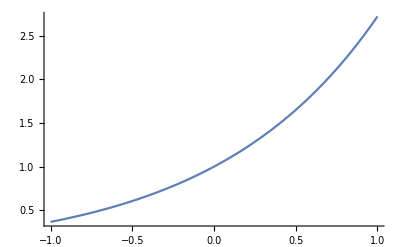

```mathematica
Plot[ⅇ^x,{x,-1,1}, PlotRange-> All]
```

```mathematica
ⅇ^(-∞)
```

0

```mathematica
ⅇ^-3413242352345243
```

1/ⅇ^3413242352345243

```mathematica
ⅇ^-3413242352345243.
```

General::munfl: Exp[-3.41324×10^15] is too small to represent as a normalized machine number; precision may be lost.

0.

Exercise 3.1

Define variables:  xa=ⅇ^a for a=153222455., xb=ⅇ^-b for  b= 153222417, and pab=xa*xb.
Find xa, xb, and pab

Answer

```mathematica
a=153222455.;
xa= ⅇ^a
```

5.130614×10^66543666

```mathematica
b= 153222417.;
xb=ⅇ^-b
```

General::munfl: Exp[-1.53222×10^8] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
pab=xa*xb
```

0.

However, if we do this:

```mathematica
a=153222455.; b= 153222417.;
pab=ⅇ^(a-b)
```

3.18559×10^16

We obtain a very different value for pab. Why?

Exercise 3.2

A 500-μF capacitor is fully charged with 10 V. At time t=0, it is allowed to suddenly discharge into a 2-kΩ resistor. What is the voltage and current at time t=1.5 sec?

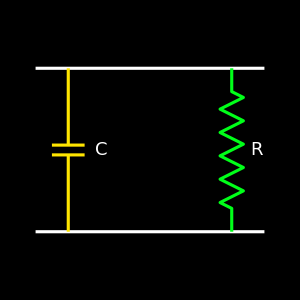

Answer

From KCL: -v_C+i R==0
       Or:      -q/c-ⅆq/ⅆt R == 0

```mathematica
DSolve[{q[t]/C+q'[t] R == 0 ,q[0]/C== v0},q[t],t]
```

{{q[t]→C ⅇ^(-t/(C R)) v0}}

Thus, voltage is:   v[t]=q[t]/C=v_0 ⅇ^(-t/(C R))
where v_0 is the initial voltage at t=0. 
The current is:  i=-q'[t]

```mathematica
q[t_]:=C ⅇ^(-t/(C R)) v0; 
-q'[t]
```

(ⅇ^(-t/(C R)) v0)/R

Thus:  i[t]=v0/R ⅇ^(-t/(C R))

Now, we can substitute:

```mathematica
Subscript[v, 0] ⅇ^(-t/(C R)) /. Subscript[v, 0]-> 10 /. C-> 500.*10^-6 /. R-> 2000 /. t-> 1.5
```

2.2313

```mathematica
Subscript[v, 0]/R ⅇ^(-t/(C R)) /. Subscript[v, 0]-> 10  /. C-> 500.*10^-6 /. R-> 2000 /. t-> 1.5
```

0.00111565

END exercise

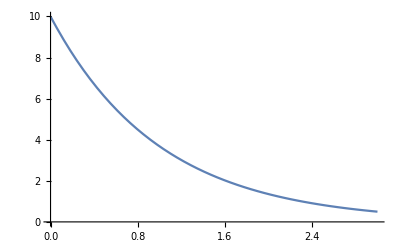

```mathematica
Plot[Subscript[v, 0] ⅇ^(-t/(C R)) /. Subscript[v, 0]-> 10/. C-> 500.*10^-6 /. R-> 2000 ,{t,0,3.}]
```

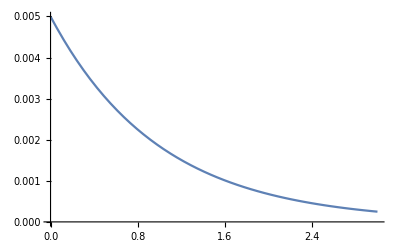

```mathematica
Plot[Subscript[v, 0]/R ⅇ^(-t/(C R)) /. Subscript[v, 0]-> 10  /. C-> 500.*10^-6 /. R-> 2000,{t,0,3.}]
```

Exercise 3.3

Find the exponential of √x for x=-2.5, using this code

```mathematica
Manipulate[ ⅇ^(√x)
,{x,-4.,4.}]
```

Answer

```mathematica
Manipulate[ ⅇ^(√x)
,{x,-4.,4.}]
```

END exercise

### 3.2 Log

```mathematica
Log[4.2]
```

1.43508

```mathematica
Log[ⅇ]
```

1

```mathematica
Log[ⅇ^15]
```

15

```mathematica
Log[0.0000473]
```

-9.959

```mathematica
Log[-3]
```

ⅈ π+Log[3]

```mathematica
Log[0]
```

-∞

```mathematica
Log[∞]
```

∞

Exercise 3.4

Find the Log of x for x=-2.5, using this code

```mathematica
Manipulate[ Log[x]
,{x,-4.,4.}]
```

Answer

```mathematica
Manipulate[ Log[x]
,{x,-4.,4.}]
```

Exercise 3.5

For circuit in Exercise 3.2, how long does it take from the moment of discharge to the time when the capacitor voltage is 2 V?

Answer

From the above, the voltage is:   v[t]== v_0 ⅇ^(-t/(C R))
then:  v[t]/v_0== ⅇ^(-t/(C R))  
And;  Log[v[t]/v_0] ==-t/(C R)  
or:    t=-R C  Log[v[t]/v_0]

```mathematica
-R C  Log[Subscript[v, 1]/Subscript[v, 0]]  /. R-> 2000. /. C-> 500.*10^-6 /. Subscript[v, 0]-> 10  /. Subscript[v, 1]-> 2
```

1.60944

It take 1.61 sec.

END exercise

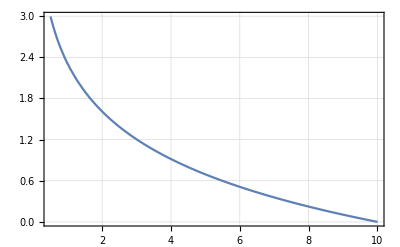

```mathematica
Plot[-R C  Log[v/Subscript[v, 0]]  /. R-> 2000. /. C-> 500.*10^-6 /. Subscript[v, 0]-> 10,{v,10.,0.5}
,Frame-> True, GridLines->Automatic]
```

### 3.3 Sinusoidal

```mathematica
Sin[0.533]
```

0.508119

```mathematica
Cos[2.531]
```

-0.819308

Exercise 3.6

Consider an AC voltage: v[t]=v_0 Cos[2 π f t]
where v0 is 120 V, f=60 Hz. What is the voltage value at t=13.5 ms.

Answer

```mathematica
Subscript[v, 0]=120.; f=60.; 
Subscript[v, 0] Cos[2 π f t] /. t-> 13.5*10^-3
```

44.1749

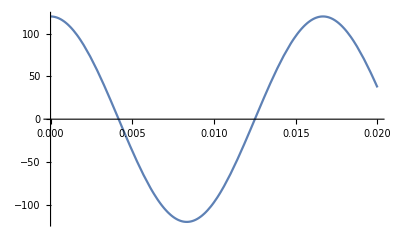

```mathematica
Plot[Subscript[v, 0] Cos[2 π f t],{t,0,0.020}]
```

Exercise 3.7

Consider an EM wave E[z,t]=E_0 Sin[2 π f (z/c-t)]
where f=2450 MHz; E_0=1. What is the E field at z=0 for t=1, 2, 3, 4 sec

Answer

```mathematica
f=2450*10^6;
Sin[2 π f (-t)] /. t-> 1.
Sin[2 π f (-t)] /. t-> 2.
Sin[2 π f (-t)] /. t-> 3.
Sin[2 π f (-t)] /. t-> 4.
```

6.73195×10^-8

1.34639×10^-7

2.10931×10^-6

2.69278×10^-7

```mathematica
f=2450*10^6;
Sin[2 π f (-t)] /. t-> 1
Sin[2 π f (-t)] /. t-> 2
Sin[2 π f (-t)] /. t-> 3
Sin[2 π f (-t)] /. t-> 4
```

0

0

0

«1 more identical outputs»

END exercise

What is the difference between the two approaches of calculation? Why the resuts are different?